# Kelvin problem in 2-d plane strain

Define the relevant functions that are needed for integrating the response to a point force

```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) 
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy)
```

-(fy (xo-xs) (-yo+ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fx ((xo-xs)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

-(fx (-xo+xs) (yo-ys))/(8 π ((xo-xs)^2+(yo-ys)^2) μ (1-ν))+(fy ((yo-ys)^2/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν))-((3-4 ν) Log[√((xo-xs)^2+(yo-ys)^2)])/(4 π (1-ν))))/(2 μ)

```mathematica
uxmod = ReplaceAll[ux,{ys->0,yo->0}];
uymod = ReplaceAll[uy,{ys->0,yo->0}];
uxint = Integrate[uxmod,{xs,-1,1},Assumptions->{Im[xo]==0}]
uyint = Integrate[uymod,{xs,-1,1},Assumptions->{Im[xo]==0}]
```

-(fx (2+1/2 (-3+4 ν) (-4-(-1+xo) Log[(-1+xo)^2]+(1+xo) Log[(1+xo)^2])))/(8 π μ (-1+ν))

(fy (-3+4 ν) (4-2 xo ArcTanh[(2 xo)/(1+xo^2)]+Log[1/((-1+xo^2)^2)]))/(16 π μ (-1+ν))

### First compute indefinite integral and then evaluate at the end points to get definite integral

```mathematica
UXindef = Integrate[ux,xs,GeneratedParameters->C];
UXdef = ReplaceAll[UXindef,{xs->1}]-ReplaceAll[UXindef,{xs->-1}];
FullSimplify[%]
```

-1/(16 π μ (-1+ν))(-16 fx (-1+ν)-8 fx (yo-ys) (-1+ν) ArcTan[(-1+xo)/(yo-ys)]+8 fx (yo-ys) (-1+ν) ArcTan[(1+xo)/(yo-ys)]+fx (-3+4 ν) Log[(-1+xo)^2+(yo-ys)^2]+(fy (-yo+ys)+fx xo (3-4 ν)) Log[1+(-2+xo) xo+(yo-ys)^2]+fx (-3+4 ν) Log[(1+xo)^2+(yo-ys)^2]+(fy (yo-ys)+fx xo (-3+4 ν)) Log[1+xo (2+xo)+(yo-ys)^2])

## Check numerical solution versus analytical solution

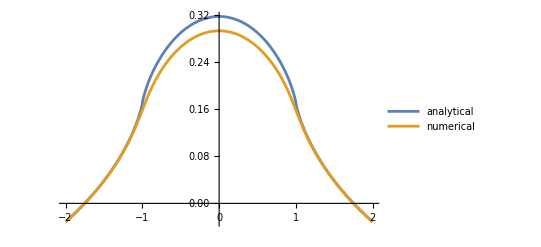

```mathematica
Plot[{ReplaceAll[uxint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[UXdef,{fx->1,fy->0,μ->1,ν->0.25,ys->0,yo->0.05}]},{xo,-2,2},PlotLegends->{"analytical","numerical"}]
```

## Plot analytical solutions for U_x and U_y

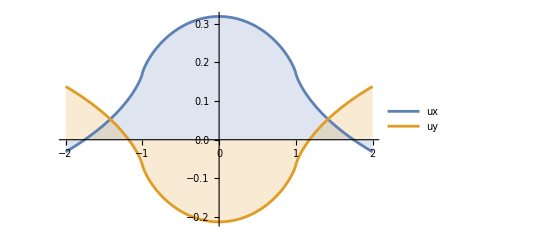

```mathematica
Plot[ {ReplaceAll[uxint,{fx -> 1,fy->0, μ->1,ν->0.25}],ReplaceAll[uyint,{fx->0,fy -> -1, μ->1,ν->0.25}]},{xo,-2,2},Filling->Axis,PlotLegends->{"ux","uy"}]
```

## Plot numerical solution for U_x in 2-d

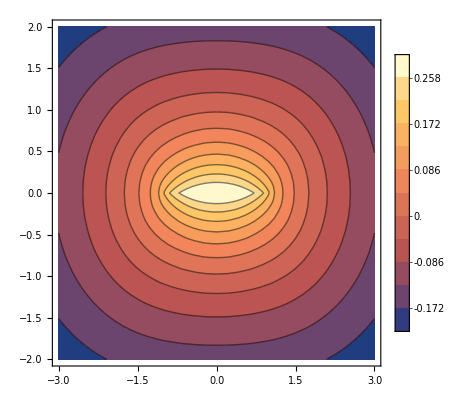

```mathematica
ContourPlot[ReplaceAll[UXdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,Contours->11]
```

## 2-d Numerical Integration

#### Integrate U_x along x_s to get a definite integral, and then compute indefinite integral over y_s, then substitute limits of y_s to get definite integral

```mathematica
UXindef2d =Integrate[ReplaceAll[UXdef,{fy->0}],ys,GeneratedParameters->C]
```

C[1]-1/(16 π μ (-1+ν))fx (12 ys-4 (1-xo) (yo-ys) (-1+ν)-4 (1+xo) (yo-ys) (-1+ν)-16 ys (-1+ν)-16 ys ν+2 (1+2 xo+xo^2) (-1+ν) ArcTan[(-1-xo)/(yo-ys)]-2 (1-2 xo+xo^2) (-1+ν) ArcTan[(1-xo)/(yo-ys)]-4 (yo-ys)^2 (-1+ν) ArcTan[(1-xo)/(yo-ys)]+2 (1-2 xo+xo^2) (-1+ν) ArcTan[(-1+xo)/(yo-ys)]-2 (1+2 xo+xo^2) (-1+ν) ArcTan[(1+xo)/(yo-ys)]-4 (yo-ys)^2 (-1+ν) ArcTan[(1+xo)/(yo-ys)]+6 (-1+xo) ArcTan[(yo-ys)/(-1+xo)]-8 (-1+xo) ν ArcTan[(yo-ys)/(-1+xo)]+2 (-1+xo) xo (-3+4 ν) ArcTan[(yo-ys)/(-1+xo)]+6 (1+xo) ArcTan[(yo-ys)/(1+xo)]-8 (1+xo) ν ArcTan[(yo-ys)/(1+xo)]-2 xo (1+xo) (-3+4 ν) ArcTan[(yo-ys)/(1+xo)]+3 (yo-ys) Log[(-1+xo)^2+(yo-ys)^2]-4 (yo-ys) ν Log[(-1+xo)^2+(yo-ys)^2]+xo (yo-ys) (-3+4 ν) Log[1-2 xo+xo^2+(yo-ys)^2]-xo (yo-ys) (-3+4 ν) Log[1+2 xo+xo^2+(yo-ys)^2]+3 (yo-ys) Log[(1+xo)^2+(yo-ys)^2]-4 (yo-ys) ν Log[(1+xo)^2+(yo-ys)^2])

-1/(16 π μ (-1+ν))fx (-4 (1-xo) yo (-1+ν)-4 (1+xo) yo (-1+ν)+2 (1+2 xo+xo^2) (-1+ν) ArcTan[(-1-xo)/yo]-2 (1-2 xo+xo^2) (-1+ν) ArcTan[(1-xo)/yo]-4 yo^2 (-1+ν) ArcTan[(1-xo)/yo]+2 (1-2 xo+xo^2) (-1+ν) ArcTan[(-1+xo)/yo]-2 (1+2 xo+xo^2) (-1+ν) ArcTan[(1+xo)/yo]-4 yo^2 (-1+ν) ArcTan[(1+xo)/yo]+6 (-1+xo) ArcTan[yo/(-1+xo)]-8 (-1+xo) ν ArcTan[yo/(-1+xo)]+2 (-1+xo) xo (-3+4 ν) ArcTan[yo/(-1+xo)]+6 (1+xo) ArcTan[yo/(1+xo)]-8 (1+xo) ν ArcTan[yo/(1+xo)]-2 xo (1+xo) (-3+4 ν) ArcTan[yo/(1+xo)]+3 yo Log[(-1+xo)^2+yo^2]-4 yo ν Log[(-1+xo)^2+yo^2]+xo yo (-3+4 ν) Log[1-2 xo+xo^2+yo^2]-xo yo (-3+4 ν) Log[1+2 xo+xo^2+yo^2]+3 yo Log[(1+xo)^2+yo^2]-4 yo ν Log[(1+xo)^2+yo^2])+1/(16 π μ (-1+ν))fx (-7.2+9.6 (-1+ν)-4 (1-xo) (0.6+yo) (-1+ν)-4 (1+xo) (0.6+yo) (-1+ν)+9.6 ν+2 (1+2 xo+xo^2) (-1+ν) ArcTan[(-1-xo)/(0.6+yo)]-2 (1-2 xo+xo^2) (-1+ν) ArcTan[(1-xo)/(0.6+yo)]-4 (0.6+yo)^2 (-1+ν) ArcTan[(1-xo)/(0.6+yo)]+2 (1-2 xo+xo^2) (-1+ν) ArcTan[(-1+xo)/(0.6+yo)]-2 (1+2 xo+xo^2) (-1+ν) ArcTan[(1+xo)/(0.6+yo)]-4 (0.6+yo)^2 (-1+ν) ArcTan[(1+xo)/(0.6+yo)]+6 (-1+xo) ArcTan[(0.6+yo)/(-1+xo)]-8 (-1+xo) ν ArcTan[(0.6+yo)/(-1+xo)]+2 (-1+xo) xo (-3+4 ν) ArcTan[(0.6+yo)/(-1+xo)]+6 (1+xo) ArcTan[(0.6+yo)/(1+xo)]-8 (1+xo) ν ArcTan[(0.6+yo)/(1+xo)]-2 xo (1+xo) (-3+4 ν) ArcTan[(0.6+yo)/(1+xo)]+3 (0.6+yo) Log[(-1+xo)^2+(0.6+yo)^2]-4 (0.6+yo) ν Log[(-1+xo)^2+(0.6+yo)^2]+xo (0.6+yo) (-3+4 ν) Log[1-2 xo+xo^2+(0.6+yo)^2]-xo (0.6+yo) (-3+4 ν) Log[1+2 xo+xo^2+(0.6+yo)^2]+3 (0.6+yo) Log[(1+xo)^2+(0.6+yo)^2]-4 (0.6+yo) ν Log[(1+xo)^2+(0.6+yo)^2])

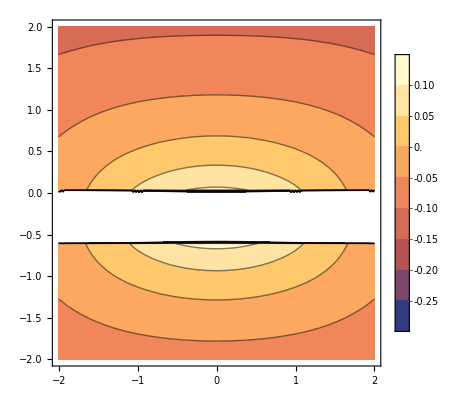

```mathematica
UXdef2d = ReplaceAll[UXindef2d,{ys->0}] - ReplaceAll[UXindef2d,{ys->-0.6}]
ContourPlot[ReplaceAll[UXdef2d,{fx->1,fy->0,μ->1,ν->0.25}],{xo,-2,2},{yo,-2,2},PlotLegends->Automatic]
```

```mathematica
Integrate[ReplaceAll[ux,{fx->1,fy->0}],xs,GeneratedParameters->C]
Integrate[ReplaceAll[UXdef,{fx->1,fy->0}],ys,GeneratedParameters->C]
Integrate[ReplaceAll[ux,{fx->1,fy->0}],xs,ys,GeneratedParameters->C]
(*uxint2 = Integrate[Integrate[ux,{xs,-1,1},Assumptions->{Im[xo]==0}],ys, Assumptions->{Im[ys]==0}]*)
(*Integrate[ux,{xs,-1,1},Assumptions->{Im[xo]==0}]*)

(*uxint2 = Integrate[Integrate[ux,{xs,-1,1}],ys]*)
(*uxint2 = Integrate[ux,xs,ys]
uxdefint2 = ReplaceAll[uxint2, {xs->1,ys->0.1}] + ReplaceAll[uxint2, {xs->-1,ys->-0.1}] - ReplaceAll[uxint2, {xs->1,ys->-0.1}] - ReplaceAll[uxint2, {xs->-1,ys->0.1}]*)
```

C[1]+1/(16 μ (π-π ν))(8 xs-8 xs ν+6 (yo-ys) ArcTan[(xo-xs)/(yo-ys)]-8 (yo-ys) ν ArcTan[(xo-xs)/(yo-ys)]-(yo-ys) ArcTan[(yo-ys)/(xo-xs)]+(yo-ys) ArcTan[(-yo+ys)/(xo-xs)]+3 (xo-xs) Log[(xo-xs)^2+(yo-ys)^2]-4 (xo-xs) ν Log[(xo-xs)^2+(yo-ys)^2])

C[1]-1/(16 π μ (-1+ν))(12 ys-4 (1-xo) (yo-ys) (-1+ν)-4 (1+xo) (yo-ys) (-1+ν)-16 ys (-1+ν)-16 ys ν+2 (1+2 xo+xo^2) (-1+ν) ArcTan[(-1-xo)/(yo-ys)]-2 (1-2 xo+xo^2) (-1+ν) ArcTan[(1-xo)/(yo-ys)]-4 (yo-ys)^2 (-1+ν) ArcTan[(1-xo)/(yo-ys)]+2 (1-2 xo+xo^2) (-1+ν) ArcTan[(-1+xo)/(yo-ys)]-2 (1+2 xo+xo^2) (-1+ν) ArcTan[(1+xo)/(yo-ys)]-4 (yo-ys)^2 (-1+ν) ArcTan[(1+xo)/(yo-ys)]+6 (-1+xo) ArcTan[(yo-ys)/(-1+xo)]-8 (-1+xo) ν ArcTan[(yo-ys)/(-1+xo)]+2 (-1+xo) xo (-3+4 ν) ArcTan[(yo-ys)/(-1+xo)]+6 (1+xo) ArcTan[(yo-ys)/(1+xo)]-8 (1+xo) ν ArcTan[(yo-ys)/(1+xo)]-2 xo (1+xo) (-3+4 ν) ArcTan[(yo-ys)/(1+xo)]+3 (yo-ys) Log[(-1+xo)^2+(yo-ys)^2]-4 (yo-ys) ν Log[(-1+xo)^2+(yo-ys)^2]+xo (yo-ys) (-3+4 ν) Log[1-2 xo+xo^2+(yo-ys)^2]-xo (yo-ys) (-3+4 ν) Log[1+2 xo+xo^2+(yo-ys)^2]+3 (yo-ys) Log[(1+xo)^2+(yo-ys)^2]-4 (yo-ys) ν Log[(1+xo)^2+(yo-ys)^2])

1/(16 μ (π-π ν))((xo xs (4-8 ν)-4 (yo-ys)^2 (-1+ν)+xo^2 (-2+4 ν)+xs^2 (-2+4 ν)) ArcTan[(yo-ys)/(xo-xs)]+(xo-xs) (4 yo-10 ys-4 yo ν+12 ys ν+(yo-ys) (-3+4 ν) Log[xo^2-2 xo xs+xs^2+(yo-ys)^2]))+C[1][ys]+C[2][xs]

```mathematica
(*Plot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25,yo->0}],{xo,-2,2}]
ContourPlot[ReplaceAll[uxdefint2,{fx -> 1,fy ->0,μ->1,ν->0.25}],{xo,-2,2},{yo,-2,2}]*)
```